## Kramers-Krönig Hilbert transform

#### Definition: “f(x)=(-2/Pi)PV Int[x*g[y]/(y^2-x^2)]dy”;

Define the KKT as a function of analytic integration on the region 0 to 2π:

#### Note - this is the imaginary to real transform!!!! not the real to imaginary

```mathematica
analyticHT[fun_,y_,upperBound_]:=Integrate[((-2y)/Pi)*fun[x]/(x^2-y^2),{x,0,upperBound},PrincipalValue->True]//N
analyticHT2[fun_,y_,upperBound_]:=Integrate[((-2y)/Pi)*fun/(x^2-y^2),{x,0,upperBound},PrincipalValue->True]//N
```

Define a numerical integration version for comparison :

```mathematica
numericalHT[fun_,y_,upperBound_,singularPointRad_,maxRecursions_,workingPrec_]:=NIntegrate[((-2y)/Pi)*fun[x]/(x^2-y^2),{x,0,upperBound},Method->{"PrincipalValue","SingularPointIntegrationRadius"->singularPointRad},MaxRecursion->maxRecursions,Exclusions->{((x^2)-(y^2))==0},WorkingPrecision->workingPrec]//N
numericalHT2[fun_,y_,upperBound_,singularPointRad_,maxRecursions_,workingPrec_]:=NIntegrate[((-2y)/Pi)*fun/(x^2-y^2),{x,0,upperBound},Method->{"PrincipalValue","SingularPointIntegrationRadius"->singularPointRad},MaxRecursion->maxRecursions,Exclusions->{((x^2)-(y^2))==0},WorkingPrecision->workingPrec]//N
```

#### Test on a simple function with known KKT, eg, cosine function:;

Note major instability issues wrt working precision and max recursions

```mathematica
Off[NIntegrate::slwcon,NIntegrate::ncvb,NIntegrate::par,NIntegrate::zeroregion]
analyticHT[Cos,2,2Pi]
numericalHT[Cos,2,2Pi,10^-10,200,55]
```

0.835679

0.835679

#### Plot to check that the cosine function KKTs to the sine function

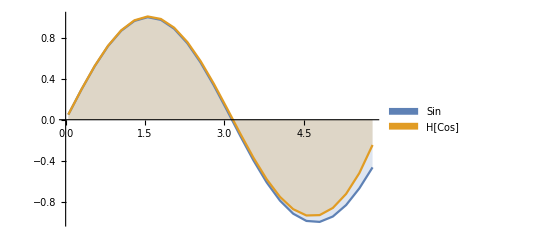

```mathematica
Off[NIntegrate::slwcon,NIntegrate::ncvb,NIntegrate::par,NIntegrate::zeroregion,NIntegrate::precw,NIntegrate::inumri,General::stop]
DiscretePlot[{Sin[y],analyticHT[Cos,y,2Pi]},{y,0.05,6,.25},AxesOrigin->{0,0},Joined->True,PlotLegends->SwatchLegend[{"Sin","H[Cos]"}]]
```

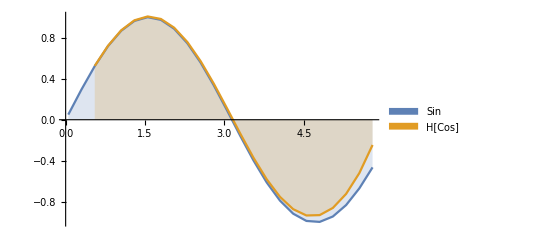

```mathematica
DiscretePlot[{Sin[y],numericalHT[Cos,y,2Pi,10^-10,200,55]},{y,0.05,6,.25},AxesOrigin->{0,0},Joined->True,PlotLegends->SwatchLegend[{"Sin","H[Cos]"}]]
```

#### Note - changing the integration upper bound to inifinty makes the Hilbert transform better at high values, but not so much at low values

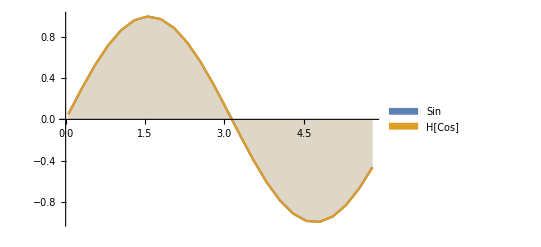

```mathematica
DiscretePlot[{Sin[y],analyticHT[Cos,y,Infinity]},{y,0.05,6,.25},AxesOrigin->{0,0},Joined->True,PlotLegends->SwatchLegend[{"Sin","H[Cos]"}]]
```

#### Check on a more realistic function, such as a cosine fitted on 20 points;

```mathematica
cosData=Table[{i*2Pi/20,Cos[i*2Pi/20]//N},{i,0,20}];
cosDataInter[x_]:=If[x>0&&x<2Pi,Interpolation[cosData][x],0]
```

```mathematica
Off[NIntegrate::eincr,General::stop]
```

```mathematica
sList=Table[Sin[i/2]//N,{i,1,12}]
hList=Table[numericalHT[cosDataInter,i/2,Infinity,10^-10,200,55],{i,1,12}]
```

{0.479426,0.841471,0.997495,0.909297,0.598472,0.14112,-0.350783,-0.756802,-0.97753,-0.958924,-0.70554,-0.279415}

{0.481589,0.845785,1.0042,0.918956,0.611931,0.159515,-0.325627,-0.721407,-0.926173,-0.879246,-0.566307,0.0481692}

#### Nice!

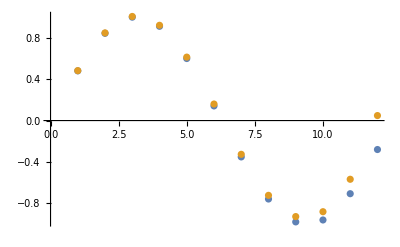

```mathematica
ListPlot[{sList,hList}]
```

## Realistic example

```mathematica
SetDirectory["/Volumes/MicroSD/Dropbox/PostDoc_SD/Conductivity_ZrC/Band_life_broadened"];
phononSE=ReadList["se.all.Gamma.Gamma-X.X.X-W.W.W-K.K.K-Gamma.Gamma-L.L",{Number, Number,Number, Number,Number, Number,Number, Number,Number, Number,Number}];
path={{0,0,0},{0,0,0},0.5({0,0,0}+{0,0.5,0.5}),{0,0.5,0.5},0.5({0,0.5,0.5}+{0.25,0.75,0.5}),{0.25,0.75,0.5},0.5({0.25,0.75,0.5}+{3/8,3/4,3/8}),{3/8,3/4,3/8},0.5({3/8,3/4,3/8}+{0,0,0}),{0,0,0},0.5({0,0,0}+{1/2,1/2,1/2}),{1/2,1/2,1/2}}
pathNorm=Table[Norm[path[[i]]-path[[i-1]]],{i,2,12}]
pathD=Table[Total@Table[pathNorm[[i]],{i,1,j}],{j,1,11}]
pList=Table[Table[pathD[[j]],{i,1,201}],{j,1,11}];
gammaData=Table[Transpose[{Transpose[phononSE][[1]],pList[[j]],Transpose[phononSE][[j+1]]}],{j,1,10}];
```

{{0,0,0},{0,0,0},{0.,0.25,0.25},{0,0.5,0.5},{0.125,0.625,0.5},{0.25,0.75,0.5},{0.3125,0.75,0.4375},{3/8,3/4,3/8},{0.1875,0.375,0.1875},{0,0,0},{0.25,0.25,0.25},{1/2,1/2,1/2}}

{0,0.353553,0.353553,0.176777,0.176777,0.0883883,0.0883883,0.459279,0.459279,0.433013,0.433013}

{0,0.353553,0.707107,0.883883,1.06066,1.14905,1.23744,1.69672,2.156,2.58901,3.02202}

```mathematica
phononSE[[1]]
```

{0.,0.,-3.07984×10^-22,2.19676×10^-22,1.3303×10^-22,1.30131×10^-22,6.12345×10^-22,-2.11556×10^-22,7.1457×10^-22,1.5268×10^-22,8.15016×10^-23}

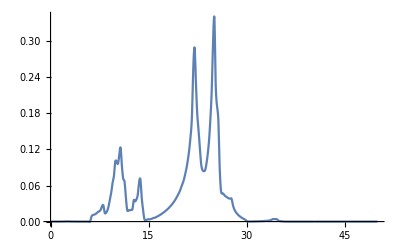

```mathematica
im[x_]:=If[0≤ x≤Transpose[gammaData[[1]]][[1]][[-1]],Interpolation[Transpose[{Transpose[gammaData[[1]]][[1]],Transpose[gammaData[[1]]][[3]]}]][x],0]
imP=Plot[im[x],{x,0,50},PlotRange->All]
```

```mathematica
imH=Table[{i,numericalHT[im,i,Infinity,10^-10,200,55]},{i,1,50}]
```

{{1,-0.00355475},{2,-0.00733053},{3,-0.0110127},{4,-0.0158459},{5,-0.0222134},{6,-0.0346481},{7,-0.0398061},{8,-0.0402596},{9,-0.0699139},{10,-0.0438722},{11,0.0398695},{12,0.0135435},{13,-0.00863692},{14,0.0407797},{15,-0.00224056},{16,-0.0208854},{17,-0.0357074},{18,-0.0497213},{19,-0.0651012},{20,-0.0835444},{21,-0.108189},{22,-0.0271872},{23,0.0652033},{24,-0.0280144},{25,0.0688155},{26,0.201573},{27,0.122854},{28,0.115809},{29,0.0937287},{30,0.0790431},{31,0.0654017},{32,0.0574594},{33,0.0514049},{34,0.0475461},{35,0.0475264},{36,0.0430914},{37,0.0399928},{38,0.0375675},{39,0.0355116},{40,0.0337229},{41,0.0321428},{42,0.0307317},{43,0.0294607},{44,0.0283079},{45,0.027256},{46,0.0262912},{47,0.0254022},{48,0.0245797},{49,0.023816},{50,0.0231045}}

InterpolatingFunction::dmval: Input value {0.00102143} lies outside the range of data in the interpolating function. Extrapolation will be used.

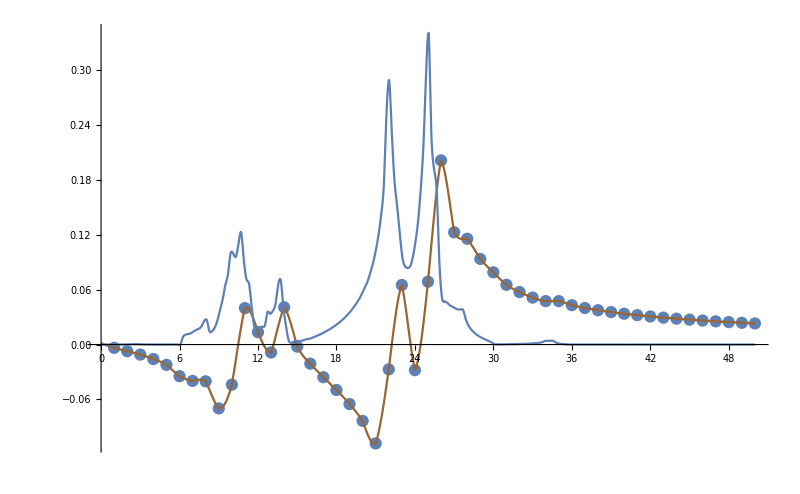

```mathematica
Show[{ListPlot[imH],Plot[Interpolation[imH][x],{x,0,50},PlotStyle->Brown],imP},PlotRange->All,ImageSize->800]
```

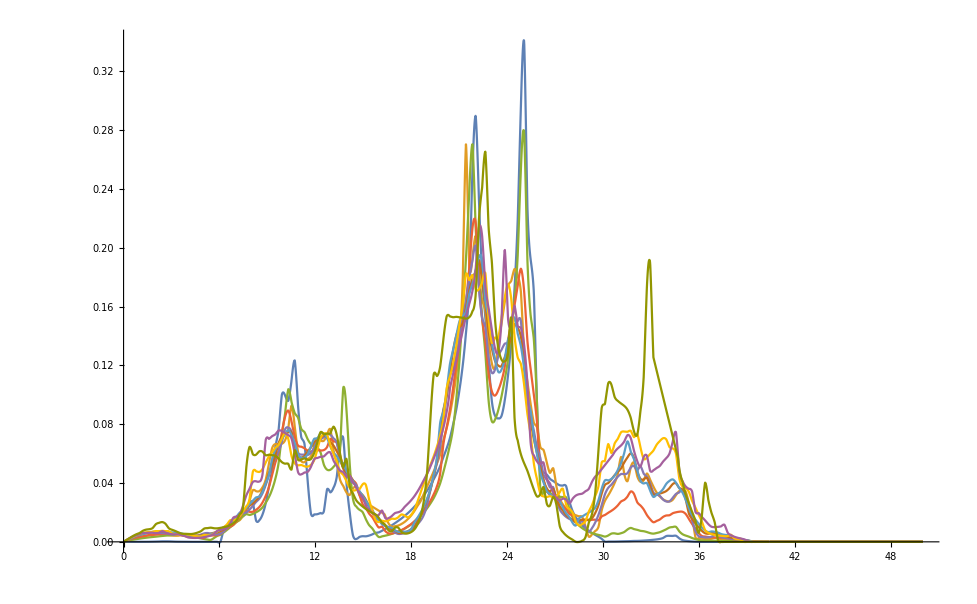

```mathematica
im[x_,part_]:=If[0≤ x≤Transpose[gammaData[[part]]][[1]][[-1]],Interpolation[Transpose[{Transpose[gammaData[[part]]][[1]],Transpose[gammaData[[part]]][[3]]}]][x],0]
imP=Plot[Evaluate@Table[im[x,i],{i,1,10}],{x,0,50},PlotRange->All]
```

```mathematica
intData=Table[{i,Integrate[im[x,i],{x,0,50}]//N},{i,1,10}]
```

{{1,1.47442},{2,1.76514},{3,1.49318},{4,1.55815},{5,1.65392},{6,1.70283},{7,1.73225},{8,1.89234},{9,1.94658},{10,2.08915}}

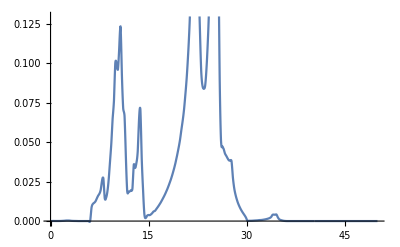

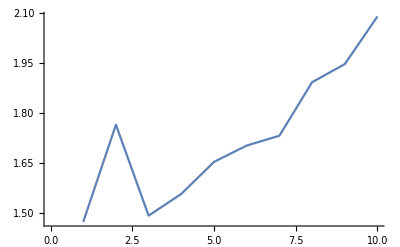

```mathematica
Plot[im[x,1],{x,0,50}]
ListLinePlot@intData
```

```mathematica
imH2=Table[{i,numericalHT2[im[x,1],i,Infinity,10^-10,20,5]},{i,1,50}]
```

NIntegrate::zeroregion: Integration region {{390000000001/10000000000,39.}} cannot be further subdivided at the specified working precision. NIntegrate assumes zero integral there and on any further indivisible regions.

{{1,-0.00339115},{2,-0.00658913},{3,-0.00994523},{4,-0.0156353},{5,-0.0221807},{6,-0.036808},{7,-0.0398498},{8,-0.0403344},{9,-0.0699198},{10,-0.0438641},{11,0.0398977},{12,0.0135349},{13,-0.00863378},{14,0.040799},{15,-0.0199799},{16,-0.0207293},{17,-0.0354608},{18,-0.049406},{19,-0.0647469},{20,-0.0805932},{21,-0.109732},{22,-0.0329396},{23,0.0627492},{24,-0.0284565},{25,0.0675276},{26,0.201367},{27,0.122736},{28,0.115753},{29,0.0937135},{30,0.0740398},{31,0.0641499},{32,0.054646},{33,0.0459418},{34,0.0276302},{35,0.0419839},{36,0.0429417},{37,0.0399928},{38,0.0375675},{39,0.0355116},{40,0.0337229},{41,0.0321428},{42,0.0307317},{43,0.0294607},{44,0.0283079},{45,0.027256},{46,0.0262912},{47,0.0254022},{48,0.0245797},{49,0.023816},{50,0.0231045}}

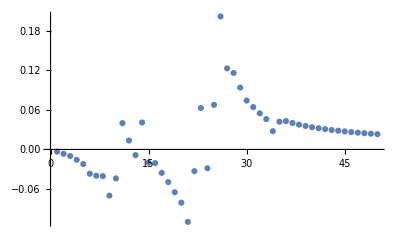

```mathematica
ListPlot@imH2
```

```mathematica
imHall=Table[{j,Table[{i,numericalHT2[im[x,j],i,Infinity,10^-10,20,5]},{i,1,50}]},{j,1,10}];
```

NIntegrate::zeroregion: Integration region {{390000000001/10000000000,39.}} cannot be further subdivided at the specified working precision. NIntegrate assumes zero integral there and on any further indivisible regions.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::zeroregion: Integration region {{390000000001/10000000000,39.}} cannot be further subdivided at the specified working precision. NIntegrate assumes zero integral there and on any further indivisible regions.

General::stop: Further output of NIntegrate::zeroregion will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

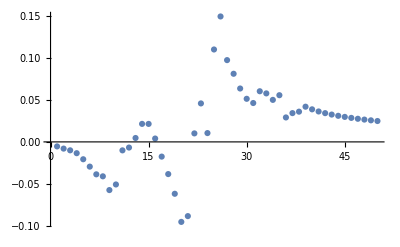

```mathematica
ListPlot@imHall[[4]][[2]]
```

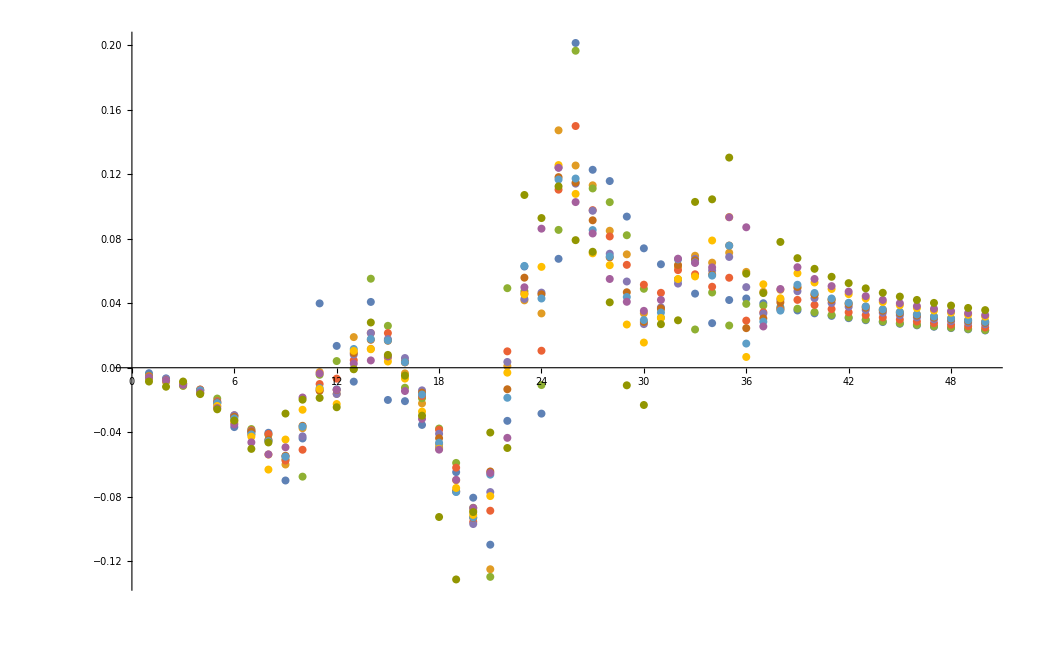

```mathematica
ListPlot[Table[imHall[[i]][[2]],{i,1,10}]]
```

```mathematica
interImHall=Table[Interpolation[imHall[[i]][[2]]],{i,1,10}]
intData=Table[Integrate[Interpolation[imHall[[i]][[2]]][x],{x,0,50}]/50,{i,1,10}]
```

{InterpolatingFunction[{{1., 50.}}, <>],InterpolatingFunction[{{1., 50.}}, <>],InterpolatingFunction[{{1., 50.}}, <>],InterpolatingFunction[{{1., 50.}}, <>],InterpolatingFunction[{{1., 50.}}, <>],InterpolatingFunction[{{1., 50.}}, <>],InterpolatingFunction[{{1., 50.}}, <>],InterpolatingFunction[{{1., 50.}}, <>],InterpolatingFunction[{{1., 50.}}, <>],InterpolatingFunction[{{1., 50.}}, <>]}

InterpolatingFunction::dmvali: The integration endpoint 0 in dimension 1 lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmvali will be suppressed during this calculation.

{0.0155382,0.018141,0.0157593,0.0163013,0.0167393,0.016596,0.016173,0.01602,0.0186953,0.0182156}

```mathematica
interImHallg0[[1]]
```

If[InterpolatingFunction[{{1., 50.}}, <>][x]>0,Interpolation[imHall⟦i⟧⟦2⟧][x],0]

```mathematica
Interpolation[imHall[[4]][[2]]][3]
If[Interpolation[imHall[[i]][[2]]][x]<0,Interpolation[imHall[[i]][[2]]][x],0]
```

-0.010061

Part::pkspec1: The expression i cannot be used as a part specification.

Interpolation::innd: First argument in i does not contain a list of data and coordinates.

If[Interpolation[i][x]<0,Interpolation[imHall⟦i⟧⟦2⟧][x],0]

```mathematica
imHall[[4]][[2]]
imHall[[5]][[2]]
```

{{1,-0.00539866},{2,-0.00800392},{3,-0.010061},{4,-0.0134856},{5,-0.0207275},{6,-0.0295358},{7,-0.0387476},{8,-0.0411257},{9,-0.0575548},{10,-0.0508617},{11,-0.0101084},{12,-0.00675772},{13,0.00465933},{14,0.02153},{15,0.0214971},{16,0.0040249},{17,-0.0175695},{18,-0.0384486},{19,-0.0619735},{20,-0.095577},{21,-0.0886637},{22,0.0101648},{23,0.0459769},{24,0.0105446},{25,0.110417},{26,0.149871},{27,0.0977153},{28,0.0814035},{29,0.0637997},{30,0.0514897},{31,0.0464516},{32,0.0605176},{33,0.05795},{34,0.0502106},{35,0.0557938},{36,0.0292185},{37,0.0343881},{38,0.0361282},{39,0.0420633},{40,0.0389158},{41,0.0363572},{42,0.0343527},{43,0.0326556},{44,0.0311775},{45,0.0298678},{46,0.0286932},{47,0.0276299},{48,0.0266601},{49,0.0257701},{50,0.024949}}

{{1,-0.00631532},{2,-0.00697699},{3,-0.00996605},{4,-0.0141918},{5,-0.021302},{6,-0.0294182},{7,-0.039315},{8,-0.0452019},{9,-0.054942},{10,-0.0425438},{11,-0.0138072},{12,-0.0163019},{13,0.00813368},{14,0.0215361},{15,0.0177674},{16,0.00601139},{17,-0.0140237},{18,-0.0409349},{19,-0.0768739},{20,-0.0969215},{21,-0.0770915},{22,0.00357699},{23,0.0426792},{24,0.0465732},{25,0.124126},{26,0.114147},{27,0.0973256},{28,0.0707039},{29,0.0534721},{30,0.0270525},{31,0.037433},{32,0.0521712},{33,0.0674957},{34,0.0602961},{35,0.0686902},{36,0.0499816},{37,0.0335821},{38,0.0422113},{39,0.0474269},{40,0.0431304},{41,0.0401458},{42,0.0377671},{43,0.0357692},{44,0.0340451},{45,0.0325303},{46,0.0311819},{47,0.0299691},{48,0.0288694},{49,0.0278651},{50,0.0269428}}

```mathematica
interRealg0[x_]:=Table[If[Interpolation[imHall[[i]][[2]]][x]>0,Interpolation[imHall[[i]][[2]]][x],0],{i,1,10}]
interReall0[x_]:=Table[If[Interpolation[imHall[[i]][[2]]][x]<0,Interpolation[imHall[[i]][[2]]][x],0],{i,1,10}]
```

```mathematica
interRealg0[15]
```

{0,0.00625274,0.025984,0.0214971,0.0177674,0.0167337,0.0169217,0.00386107,0.00696739,0.00795199}

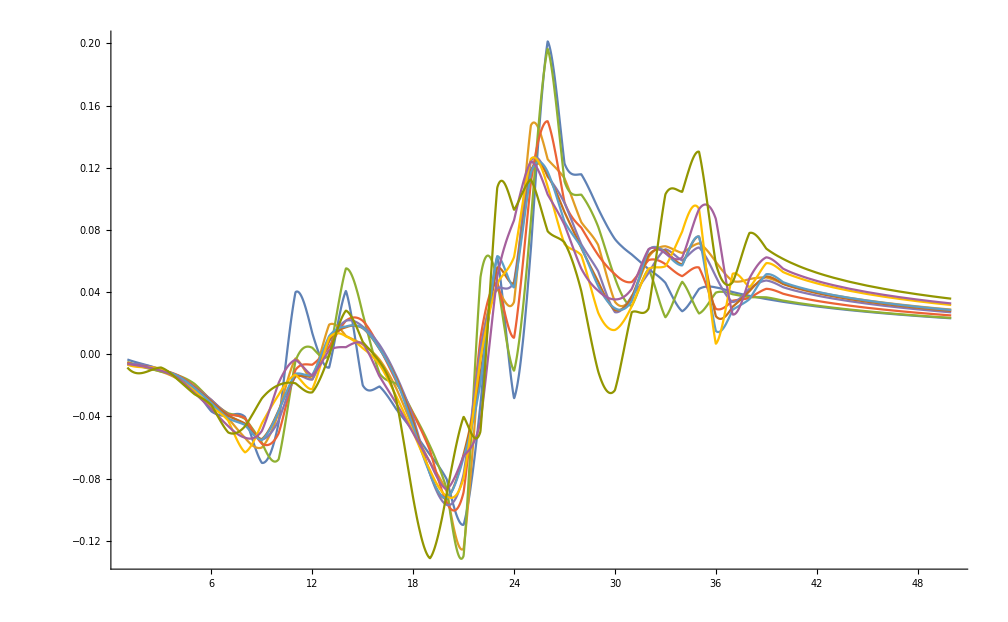

```mathematica
Plot[Evaluate@Table[interImHall[[i]][x],{i,1,10}],{x,1,50}]
```

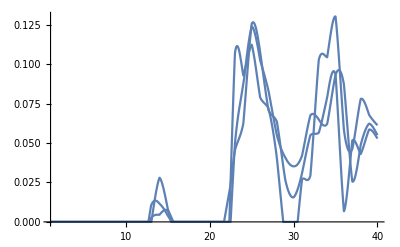

```mathematica
Plot[Table[interRealg0[x][[i]],{i,8,10}],{x,1,40}]
```

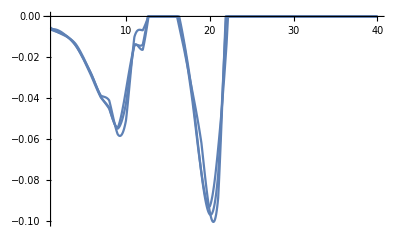

```mathematica
Plot[Table[interReall0[x][[i]],{i,4,6}],{x,1,40}]
```

```mathematica
"Gamma.Gamma-X.X.X-W.W.W-K.K.K-Gamma.Gamma-L.L"
```

```mathematica
im[x_]:=If[0≤ x≤Transpose[gammaData[[1]]][[1]][[-1]],Interpolation[Transpose[{Transpose[gammaData[[1]]][[1]],Transpose[gammaData[[1]]][[3]]}]][x],0]
imP=Plot[im[x],{x,0,50},PlotRange->All]
```

-Graphics-

```mathematica
popts3D={BoxRatios->{1.5,1,0.6},Filling->Bottom,PlotTheme->"Scientific",AxesLabel->{Style["ω (THz)",18,Black],Style["q (1/Å)",18,Black],Style["Γ''(ω,q)  ",18,Black]" \n(THz)  "},AxesStyle->Directive[18,Black,Thickness[0.004]],Boxed->False,BoxStyle->Directive[Thickness[0.00001],Dashing[0.02]],PlotStyle->Directive[Black,PointSize[0.006]],Ticks->{{10,20,30},{{0,"Γ"},{0.35,"Γ-X"},{0.7,"X"},{0.83,""},{1.00,"W"},{1.15,""},{1.3,"K"},{1.7,"K-Γ"},{2.1,"Γ-L"},{2.6,"L"}},Automatic
},FillingStyle->Directive[Thickness[1],Orange,Thin,Opacity[1]],ImageSize->850,PlotRange->{{5,38},Full,{0,0.26}}};
```

```mathematica
gammaData=Table[Transpose[{Transpose[phononSE][[1]],pList[[j]],Transpose[phononSE][[j+1]]}],{j,1,10}];
```

```mathematica
"Triplets: Energy, position, GammaSE"
qPointList={0,0.35,0.71,0.88,1.06,1.15,1.23,1.7,2.15,2.589}
```

Triplets: Energy, position, GammaSE

{0,0.35,0.71,0.88,1.06,1.15,1.23,1.7,2.15,2.589}

```mathematica
qPointList
```

{0,0.35,0.71,0.88,1.06,1.15,1.23,1.7,2.15,2.589}

```mathematica
interImHall[[1]]
```

```mathematica
"Gamma at different energies for q point 1";
realGammaData=Table[Table[{Transpose[gammaData[[j]]][[1]][[i]],qPointList[[j]],interImHall[[1]][Transpose[gammaData[[j]]][[1]][[i]]]},{i,1,Length[Transpose[gammaData[[j]]][[1]]]}],{j,1,Length[qPointList]}];
```

InterpolatingFunction::dmval: Input value {0.} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.202083} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.404167} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
realGammaDataDw=Table[Table[{Transpose[gammaData[[j]]][[1]][[i]],qPointList[[j]],interReall0[Transpose[gammaData[[j]]][[1]][[i]]][[j]]},{i,1,Length[Transpose[gammaData[[j]]][[1]]]}],{j,1,Length[qPointList]}];
```

InterpolatingFunction::dmval: Input value {0.} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
realGammaDataUp=Table[Table[{Transpose[gammaData[[j]]][[1]][[i]],qPointList[[j]],interRealg0[Transpose[gammaData[[j]]][[1]][[i]]][[j]]},{i,1,Length[Transpose[gammaData[[j]]][[1]]]}],{j,1,Length[qPointList]}];
```

InterpolatingFunction::dmval: Input value {0.} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
popts3Dreal={BoxRatios->{1.5,1,0.6},PlotTheme->"Scientific",AxesLabel->{Style["ω (THz)",18,Black],Style["q (1/Å)",18,Black],Style["Γ''(ω,q)  ",18,Black]" \n(THz)  "},AxesStyle->Directive[18,Black,Thickness[0.004]],Boxed->False,BoxStyle->Directive[Thickness[0.00001],Dashing[0.02]],PlotStyle->Directive[Black,PointSize[0.006]],Ticks->{{10,20,30},{{0,"Γ"},{0.35,"Γ-X"},{0.7,"X"},{0.83,""},{1.00,"W"},{1.15,""},{1.3,"K"},{1.7,"K-Γ"},{2.1,"Γ-L"},{2.6,"L"}},Automatic
},Filling->Axis,FillingStyle->{Orange,Blue},ImageSize->850,PlotRange->{{5,38},{0,3},{-0.11,0.2}}};
ListPointPlot3D[realGammaData,ImageSize->500,Evaluate@popts3Dreal]/.Point[a___]:>{Thickness[0.004],Line[a]}
```

-Graphics3D-

```mathematica
p1=ListPointPlot3D[gammaData,ImageSize->500,Evaluate@popts3D]/.Point[a___]:>{Thickness[0.004],Line[a]}
```

-Graphics3D-

```mathematica
popts3Dreal1={BoxRatios->{1.5,1,0.6},PlotTheme->"Scientific",AxesLabel->{Style["ω (THz)",18,Black],Style["q (1/Å)",18,Black],Style["Γ'(ω,q)  ",18,Black]" \n(THz)  "},AxesStyle->Directive[18,Black,Thickness[0.004]],Boxed->False,BoxStyle->Directive[Thickness[0.00001],Dashing[0.02]],PlotStyle->Directive[Black,PointSize[0.006]],Ticks->{{10,20,30},{{0,"Γ"},{0.35,"Γ-X"},{0.7,"X"},{0.83,""},{1.00,"W"},{1.15,""},{1.3,"K"},{1.7,"K-Γ"},{2.1,"Γ-L"},{2.6,"L"}},Automatic
},Filling->Axis,FillingStyle->{Orange},ImageSize->850,PlotRange->{{5,38},{0,3},{-0.11,0.2}}};
p2=ListPointPlot3D[realGammaData,ImageSize->500,Evaluate@popts3Dreal1]/.Point[a___]:>{Thickness[0.004],Line[a]}
```

-Graphics3D-

```mathematica
GraphicsGrid[{{p1,p2}},ImageSize->1000]
```

-Graphics-